```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,28000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,0.267,0,7]},{ω,Range[-0.8,0.8,0.001]}]
```

{{-0.8,1.5052×10^-6},{-0.799,1.58486×10^-6},{-0.798,1.67101×10^-6},{-0.797,1.76437×10^-6},{-0.796,1.86578×10^-6},{-0.795,1.97618×10^-6},{-0.794,2.09666×10^-6},{-0.793,2.22849×10^-6},{-0.792,2.37314×10^-6},{-0.791,2.53231×10^-6},{-0.79,2.70801×10^-6},{-0.789,2.90262×10^-6},{-0.788,3.11892×10^-6},{-0.787,3.36026×10^-6},{-0.786,3.63064×10^-6},{-0.785,3.93491×10^-6},{-0.784,4.27895×10^-6},{-0.783,4.66997×10^-6},{-0.782,5.11692×10^-6},{-0.781,5.63095×10^-6},{-0.78,6.22612×10^-6},{-0.779,6.92041×10^-6},{-0.778,7.73701×10^-6},{-0.777,8.70633×10^-6},{-0.776,9.86882×10^-6},{-0.775,0.0000112792},{-0.774,0.0000130131},{-0.773,0.0000151772},{-0.772,0.000017926},{-0.771,0.0000214898},{-0.77,0.0000262249},{-0.769,0.0000327048},{-0.768,0.0000419025},{-0.767,0.0000555752},{-0.766,0.0000771673},{-0.765,0.000114202},{-0.764,0.000185813},{-0.763,0.000353381},{-0.762,0.000913189},{-0.761,0.00583225},{-0.76,0.980913},{-0.759,0.998632},{-0.758,0.999545},{-0.757,0.999775},{-0.756,0.999866},{-0.755,0.999911},{-0.754,0.999937},{-0.753,0.999953},{-0.752,0.999963},{-0.751,0.999971},{-0.75,0.999976},{-0.749,0.99998},{-0.748,0.999983},{-0.747,0.999986},{-0.746,0.999988},{-0.745,0.999989},{-0.744,0.99999},{-0.743,0.999991},{-0.742,0.999992},{-0.741,0.999993},{-0.74,0.999994},{-0.739,0.999994},{-0.738,0.999995},{-0.737,0.999995},{-0.736,0.999996},{-0.735,0.999996},{-0.734,0.999996},{-0.733,0.999997},{-0.732,0.999997},{-0.731,0.999997},{-0.73,0.999997},{-0.729,0.999998},{-0.728,0.999998},{-0.727,0.999998},{-0.726,0.999998},{-0.725,0.999998},{-0.724,0.999998},{-0.723,0.999998},{-0.722,0.999998},{-0.721,0.999999},{-0.72,0.999999},{-0.719,0.999999},{-0.718,0.999999},{-0.717,0.999999},{-0.716,0.999999},{-0.715,0.999999},{-0.714,0.999999},{-0.713,0.999999},{-0.712,0.999999},{-0.711,0.999999},{-0.71,0.999999},{-0.709,0.999999},{-0.708,0.999999},{-0.707,1.},{-0.706,1.},{-0.705,1.},{-0.704,1.},{-0.703,1.},{-0.702,1.},{-0.701,1.},{-0.7,1.},{-0.699,1.},{-0.698,1.},{-0.697,1.},{-0.696,1.},{-0.695,1.},{-0.694,1.},{-0.693,1.},{-0.692,1.},{-0.691,1.},{-0.69,1.},{-0.689,1.},{-0.688,1.},{-0.687,1.},{-0.686,1.},{-0.685,1.},{-0.684,1.},{-0.683,1.},{-0.682,1.},{-0.681,1.},{-0.68,1.},{-0.679,1.},{-0.678,1.},{-0.677,1.},{-0.676,1.},{-0.675,1.},{-0.674,1.},{-0.673,1.},{-0.672,1.},{-0.671,1.},{-0.67,1.},{-0.669,1.},{-0.668,1.},{-0.667,1.},{-0.666,1.},{-0.665,1.00001},{-0.664,1.00001},{-0.663,1.00001},{-0.662,1.00001},{-0.661,1.00001},{-0.66,1.00001},{-0.659,1.00001},{-0.658,1.00001},{-0.657,1.00002},{-0.656,1.00002},{-0.655,1.00002},{-0.654,1.00003},{-0.653,1.00003},{-0.652,1.00004},{-0.651,1.00006},{-0.65,1.00008},{-0.649,1.00013},{-0.648,1.00021},{-0.647,1.00043},{-0.646,1.00126},{-0.645,1.01456},{-0.644,1.99307},{-0.643,1.99902},{-0.642,1.99963},{-0.641,1.9998},{-0.64,1.99988},{-0.639,1.99992},{-0.638,1.99994},{-0.637,1.99996},{-0.636,1.99997},{-0.635,1.99997},{-0.634,1.99998},{-0.633,1.99998},{-0.632,1.99998},{-0.631,1.99999},{-0.63,1.99999},{-0.629,1.99999},{-0.628,1.99999},{-0.627,1.99999},{-0.626,1.99999},{-0.625,1.99999},{-0.624,1.99999},{-0.623,1.99999},{-0.622,1.99999},{-0.621,2.},{-0.62,2.},{-0.619,2.},{-0.618,2.},{-0.617,2.},{-0.616,2.},{-0.615,2.},{-0.614,2.},{-0.613,2.},{-0.612,2.},{-0.611,2.},{-0.61,2.},{-0.609,2.},{-0.608,2.},{-0.607,2.},{-0.606,2.},{-0.605,2.},{-0.604,2.},{-0.603,2.},{-0.602,2.},{-0.601,2.},{-0.6,2.},{-0.599,2.},{-0.598,2.},{-0.597,2.},{-0.596,2.},{-0.595,2.},{-0.594,2.},{-0.593,2.},{-0.592,2.},{-0.591,2.},{-0.59,2.},{-0.589,2.},{-0.588,2.},{-0.587,2.},{-0.586,2.},{-0.585,2.},{-0.584,2.},{-0.583,2.},{-0.582,2.},{-0.581,2.},{-0.58,2.},{-0.579,2.},{-0.578,2.},{-0.577,2.},{-0.576,2.},{-0.575,2.},{-0.574,2.},{-0.573,2.},{-0.572,2.},{-0.571,2.},{-0.57,2.},{-0.569,2.},{-0.568,2.},{-0.567,2.},{-0.566,2.},{-0.565,2.},{-0.564,2.},{-0.563,2.},{-0.562,2.},{-0.561,2.},{-0.56,2.},{-0.559,2.},{-0.558,2.},{-0.557,2.},{-0.556,2.},{-0.555,2.},{-0.554,2.},{-0.553,2.},{-0.552,2.},{-0.551,2.},{-0.55,2.},{-0.549,2.},{-0.548,2.},{-0.547,2.},{-0.546,2.},{-0.545,2.},{-0.544,2.},{-0.543,2.},{-0.542,2.},{-0.541,2.},{-0.54,2.},{-0.539,2.},{-0.538,2.},{-0.537,2.},{-0.536,2.},{-0.535,2.},{-0.534,2.},{-0.533,2.},{-0.532,2.},{-0.531,2.},{-0.53,2.},{-0.529,2.},{-0.528,2.},{-0.527,2.},{-0.526,2.},{-0.525,2.},{-0.524,2.},{-0.523,2.},{-0.522,2.},{-0.521,2.},{-0.52,2.},{-0.519,2.},{-0.518,2.},{-0.517,2.},{-0.516,2.},{-0.515,2.},{-0.514,2.},{-0.513,2.},{-0.512,2.},{-0.511,2.},{-0.51,2.},{-0.509,2.},{-0.508,2.},{-0.507,2.},{-0.506,2.},{-0.505,2.},{-0.504,2.},{-0.503,2.},{-0.502,2.},{-0.501,2.},{-0.5,2.},{-0.499,2.},{-0.498,2.},{-0.497,2.},{-0.496,2.},{-0.495,2.},{-0.494,2.},{-0.493,2.},{-0.492,2.00001},{-0.491,2.00001},{-0.49,2.00001},{-0.489,2.00001},{-0.488,2.00001},{-0.487,2.00001},{-0.486,2.00001},{-0.485,2.00001},{-0.484,2.00002},{-0.483,2.00002},{-0.482,2.00002},{-0.481,2.00003},{-0.48,2.00003},{-0.479,2.00004},{-0.478,2.00006},{-0.477,2.00008},{-0.476,2.00011},{-0.475,2.00019},{-0.474,2.00036},{-0.473,2.00092},{-0.472,2.00586},{-0.471,2.98106},{-0.47,2.99864},{-0.469,2.99955},{-0.468,2.99978},{-0.467,2.99987},{-0.466,2.99991},{-0.465,2.99994},{-0.464,2.99995},{-0.463,2.99996},{-0.462,2.99997},{-0.461,2.99998},{-0.46,2.99998},{-0.459,2.99998},{-0.458,2.99999},{-0.457,2.99999},{-0.456,2.99999},{-0.455,2.99999},{-0.454,2.99999},{-0.453,2.99999},{-0.452,2.99999},{-0.451,2.99999},{-0.45,2.99999},{-0.449,2.99999},{-0.448,3.},{-0.447,3.},{-0.446,3.},{-0.445,3.},{-0.444,3.},{-0.443,3.},{-0.442,3.},{-0.441,3.},{-0.44,3.},{-0.439,3.},{-0.438,3.},{-0.437,3.},{-0.436,3.},{-0.435,3.},{-0.434,3.},{-0.433,3.},{-0.432,3.},{-0.431,3.},{-0.43,3.},{-0.429,3.},{-0.428,3.},{-0.427,3.},{-0.426,3.},{-0.425,3.},{-0.424,3.},{-0.423,3.},{-0.422,3.},{-0.421,3.},{-0.42,3.},{-0.419,3.},{-0.418,3.},{-0.417,3.},{-0.416,3.},{-0.415,3.},{-0.414,3.},{-0.413,3.},{-0.412,3.},{-0.411,3.},{-0.41,3.},{-0.409,3.},{-0.408,3.},{-0.407,3.},{-0.406,3.},{-0.405,3.},{-0.404,3.},{-0.403,3.},{-0.402,3.},{-0.401,3.},{-0.4,3.},{-0.399,3.},{-0.398,3.},{-0.397,3.},{-0.396,3.},{-0.395,3.},{-0.394,3.},{-0.393,3.},{-0.392,3.},{-0.391,3.},{-0.39,3.},{-0.389,3.},{-0.388,3.},{-0.387,3.},{-0.386,3.},{-0.385,3.},{-0.384,3.},{-0.383,3.},{-0.382,3.},{-0.381,3.},{-0.38,3.},{-0.379,3.},{-0.378,3.},{-0.377,3.},{-0.376,3.},{-0.375,3.},{-0.374,3.},{-0.373,3.},{-0.372,3.},{-0.371,3.},{-0.37,3.},{-0.369,3.},{-0.368,3.},{-0.367,3.},{-0.366,3.},{-0.365,3.},{-0.364,3.},{-0.363,3.},{-0.362,3.},{-0.361,3.},{-0.36,3.},{-0.359,3.},{-0.358,3.},{-0.357,3.},{-0.356,3.},{-0.355,3.},{-0.354,3.},{-0.353,3.},{-0.352,3.},{-0.351,3.},{-0.35,3.},{-0.349,3.},{-0.348,3.},{-0.347,3.},{-0.346,3.},{-0.345,3.},{-0.344,3.},{-0.343,3.},{-0.342,3.},{-0.341,3.},{-0.34,3.},{-0.339,3.},{-0.338,3.},{-0.337,3.},{-0.336,3.},{-0.335,3.},{-0.334,3.},{-0.333,3.},{-0.332,3.},{-0.331,3.},{-0.33,3.},{-0.329,3.},{-0.328,3.},{-0.327,3.},{-0.326,3.},{-0.325,3.},{-0.324,3.},{-0.323,3.},{-0.322,3.},{-0.321,3.},{-0.32,3.},{-0.319,3.},{-0.318,3.},{-0.317,3.},{-0.316,3.},{-0.315,3.},{-0.314,3.},{-0.313,3.},{-0.312,3.},{-0.311,3.},{-0.31,3.},{-0.309,3.},{-0.308,3.},{-0.307,3.},{-0.306,3.},{-0.305,3.},{-0.304,3.},{-0.303,3.},{-0.302,3.},{-0.301,3.},{-0.3,3.},{-0.299,3.},{-0.298,3.},{-0.297,3.},{-0.296,3.},{-0.295,3.},{-0.294,3.},{-0.293,3.},{-0.292,3.},{-0.291,3.},{-0.29,3.},{-0.289,3.},{-0.288,3.},{-0.287,3.},{-0.286,3.},{-0.285,3.},{-0.284,3.},{-0.283,3.},{-0.282,3.},{-0.281,3.},{-0.28,3.},{-0.279,3.},{-0.278,3.},{-0.277,3.},{-0.276,3.},{-0.275,3.},{-0.274,3.},{-0.273,3.},{-0.272,3.},{-0.271,3.},{-0.27,3.},{-0.269,3.},{-0.268,3.},{-0.267,3.},{-0.266,3.},{-0.265,3.},{-0.264,3.},{-0.263,3.},{-0.262,3.},{-0.261,3.},{-0.26,3.},{-0.259,3.},{-0.258,3.},{-0.257,3.},{-0.256,3.},{-0.255,3.},{-0.254,3.},{-0.253,3.},{-0.252,3.},{-0.251,3.},{-0.25,3.},{-0.249,2.99999},{-0.248,2.99999},{-0.247,2.99999},{-0.246,2.99999},{-0.245,2.99999},{-0.244,2.99999},{-0.243,2.99999},{-0.242,2.99999},{-0.241,2.99999},{-0.24,2.99999},{-0.239,2.99998},{-0.238,2.99998},{-0.237,2.99998},{-0.236,2.99997},{-0.235,2.99997},{-0.234,2.99996},{-0.233,2.99994},{-0.232,2.99992},{-0.231,2.99988},{-0.23,2.99981},{-0.229,2.99964},{-0.228,2.99908},{-0.227,2.99415},{-0.226,2.01906},{-0.225,2.00136},{-0.224,2.00045},{-0.223,2.00022},{-0.222,2.00013},{-0.221,2.00009},{-0.22,2.00006},{-0.219,2.00005},{-0.218,2.00004},{-0.217,2.00003},{-0.216,2.00002},{-0.215,2.00002},{-0.214,2.00002},{-0.213,2.00001},{-0.212,2.00001},{-0.211,2.00001},{-0.21,2.00001},{-0.209,2.00001},{-0.208,2.00001},{-0.207,2.00001},{-0.206,2.00001},{-0.205,2.00001},{-0.204,2.},{-0.203,2.},{-0.202,2.},{-0.201,2.},{-0.2,2.},{-0.199,2.},{-0.198,2.},{-0.197,2.},{-0.196,2.},{-0.195,2.},{-0.194,2.},{-0.193,2.},{-0.192,2.},{-0.191,2.},{-0.19,2.},{-0.189,2.},{-0.188,2.},{-0.187,2.},{-0.186,2.},{-0.185,2.},{-0.184,2.},{-0.183,2.},{-0.182,2.},{-0.181,2.},{-0.18,2.},{-0.179,2.},{-0.178,2.},{-0.177,2.},{-0.176,2.},{-0.175,2.},{-0.174,2.},{-0.173,2.},{-0.172,2.},{-0.171,2.},{-0.17,2.},{-0.169,2.},{-0.168,2.},{-0.167,2.},{-0.166,2.},{-0.165,2.},{-0.164,2.},{-0.163,2.},{-0.162,2.},{-0.161,2.},{-0.16,2.},{-0.159,2.},{-0.158,2.},{-0.157,2.},{-0.156,2.},{-0.155,2.},{-0.154,2.},{-0.153,2.},{-0.152,2.},{-0.151,2.},{-0.15,2.},{-0.149,2.},{-0.148,2.},{-0.147,2.},{-0.146,2.},{-0.145,2.},{-0.144,2.},{-0.143,2.},{-0.142,2.},{-0.141,2.},{-0.14,2.},{-0.139,2.},{-0.138,2.},{-0.137,2.},{-0.136,2.},{-0.135,2.},{-0.134,2.},{-0.133,2.},{-0.132,1.99999},{-0.131,1.99999},{-0.13,1.99999},{-0.129,1.99999},{-0.128,1.99999},{-0.127,1.99999},{-0.126,1.99999},{-0.125,1.99999},{-0.124,1.99999},{-0.123,1.99998},{-0.122,1.99998},{-0.121,1.99998},{-0.12,1.99997},{-0.119,1.99997},{-0.118,1.99996},{-0.117,1.99994},{-0.116,1.99992},{-0.115,1.99987},{-0.114,1.99979},{-0.113,1.99957},{-0.112,1.99874},{-0.111,1.98544},{-0.11,1.00693},{-0.109,1.00098},{-0.108,1.00037},{-0.107,1.0002},{-0.106,1.00012},{-0.105,1.00008},{-0.104,1.00006},{-0.103,1.00004},{-0.102,1.00003},{-0.101,1.00003},{-0.1,1.00002},{-0.099,1.00002},{-0.098,1.00002},{-0.097,1.00001},{-0.096,1.00001},{-0.095,1.00001},{-0.094,1.00001},{-0.093,1.00001},{-0.092,1.00001},{-0.091,1.00001},{-0.09,1.},{-0.089,1.},{-0.088,1.},{-0.087,1.},{-0.086,1.},{-0.085,1.},{-0.084,1.},{-0.083,1.},{-0.082,0.999999},{-0.081,0.999999},{-0.08,0.999998},{-0.079,0.999997},{-0.078,0.999996},{-0.077,0.999994},{-0.076,0.999993},{-0.075,0.99999},{-0.074,0.999988},{-0.073,0.999984},{-0.072,0.999979},{-0.071,0.999973},{-0.07,0.999963},{-0.069,0.999949},{-0.068,0.999925},{-0.067,0.999883},{-0.066,0.999797},{-0.065,0.999576},{-0.064,0.998686},{-0.063,0.981233},{-0.062,0.00596249},{-0.061,0.000958421},{-0.06,0.000381714},{-0.059,0.00020676},{-0.058,0.00013098},{-0.057,0.0000912608},{-0.056,0.0000677918},{-0.055,0.0000527313},{-0.054,0.0000424649},{-0.053,0.000035136},{-0.052,0.0000297101},{-0.051,0.0000255729},{-0.05,0.0000223406},{-0.049,0.0000197634},{-0.048,0.0000176724},{-0.047,0.0000159504},{-0.046,0.0000145138},{-0.045,0.0000133015},{-0.044,0.0000122684},{-0.043,0.00001138},{-0.042,0.0000106099},{-0.041,9.93779×10^-6},{-0.04,9.3473×10^-6},{-0.039,8.82557×10^-6},{-0.038,8.36218×10^-6},{-0.037,7.94867×10^-6},{-0.036,7.57808×10^-6},{-0.035,7.24468×10^-6},{-0.034,6.94368×10^-6},{-0.033,6.67106×10^-6},{-0.032,6.42344×10^-6},{-0.031,6.19793×10^-6},{-0.03,5.99208×10^-6},{-0.029,5.8038×10^-6},{-0.028,5.63126×10^-6},{-0.027,5.47289×10^-6},{-0.026,5.32734×10^-6},{-0.025,5.19341×10^-6},{-0.024,5.07006×10^-6},{-0.023,4.95638×10^-6},{-0.022,4.85157×10^-6},{-0.021,4.75492×10^-6},{-0.02,4.6658×10^-6},{-0.019,4.58365×10^-6},{-0.018,4.50799×10^-6},{-0.017,4.43837×10^-6},{-0.016,4.3744×10^-6},{-0.015,4.31574×10^-6},{-0.014,4.26208×10^-6},{-0.013,4.21315×10^-6},{-0.012,4.1687×10^-6},{-0.011,4.12851×10^-6},{-0.01,4.0924×10^-6},{-0.009,4.06019×10^-6},{-0.008,4.03174×10^-6},{-0.007,4.00693×10^-6},{-0.006,3.98563×10^-6},{-0.005,3.96776×10^-6},{-0.004,3.95325×10^-6},{-0.003,3.94202×10^-6},{-0.002,3.93403×10^-6},{-0.001,3.92926×10^-6},{0.,3.92767×10^-6},{0.001,3.92926×10^-6},{0.002,3.93403×10^-6},{0.003,3.94202×10^-6},{0.004,3.95325×10^-6},{0.005,3.96776×10^-6},{0.006,3.98563×10^-6},{0.007,4.00693×10^-6},{0.008,4.03174×10^-6},{0.009,4.06019×10^-6},{0.01,4.0924×10^-6},{0.011,4.12851×10^-6},{0.012,4.1687×10^-6},{0.013,4.21315×10^-6},{0.014,4.26208×10^-6},{0.015,4.31574×10^-6},{0.016,4.3744×10^-6},{0.017,4.43837×10^-6},{0.018,4.50799×10^-6},{0.019,4.58365×10^-6},{0.02,4.6658×10^-6},{0.021,4.75492×10^-6},{0.022,4.85157×10^-6},{0.023,4.95638×10^-6},{0.024,5.07006×10^-6},{0.025,5.19341×10^-6},{0.026,5.32734×10^-6},{0.027,5.47289×10^-6},{0.028,5.63126×10^-6},{0.029,5.8038×10^-6},{0.03,5.99208×10^-6},{0.031,6.19793×10^-6},{0.032,6.42344×10^-6},{0.033,6.67106×10^-6},{0.034,6.94368×10^-6},{0.035,7.24468×10^-6},{0.036,7.57808×10^-6},{0.037,7.94867×10^-6},{0.038,8.36218×10^-6},{0.039,8.82557×10^-6},{0.04,9.3473×10^-6},{0.041,9.93779×10^-6},{0.042,0.0000106099},{0.043,0.00001138},{0.044,0.0000122684},{0.045,0.0000133015},{0.046,0.0000145138},{0.047,0.0000159504},{0.048,0.0000176724},{0.049,0.0000197634},{0.05,0.0000223406},{0.051,0.0000255729},{0.052,0.0000297101},{0.053,0.000035136},{0.054,0.0000424649},{0.055,0.0000527313},{0.056,0.0000677918},{0.057,0.0000912608},{0.058,0.00013098},{0.059,0.00020676},{0.06,0.000381714},{0.061,0.000958421},{0.062,0.00596249},{0.063,0.981233},{0.064,0.998686},{0.065,0.999576},{0.066,0.999797},{0.067,0.999883},{0.068,0.999925},{0.069,0.999949},{0.07,0.999963},{0.071,0.999973},{0.072,0.999979},{0.073,0.999984},{0.074,0.999988},{0.075,0.99999},{0.076,0.999993},{0.077,0.999994},{0.078,0.999996},{0.079,0.999997},{0.08,0.999998},{0.081,0.999999},{0.082,0.999999},{0.083,1.},{0.084,1.},{0.085,1.},{0.086,1.},{0.087,1.},{0.088,1.},{0.089,1.},{0.09,1.},{0.091,1.00001},{0.092,1.00001},{0.093,1.00001},{0.094,1.00001},{0.095,1.00001},{0.096,1.00001},{0.097,1.00001},{0.098,1.00002},{0.099,1.00002},{0.1,1.00002},{0.101,1.00003},{0.102,1.00003},{0.103,1.00004},{0.104,1.00006},{0.105,1.00008},{0.106,1.00012},{0.107,1.0002},{0.108,1.00037},{0.109,1.00098},{0.11,1.00693},{0.111,1.98544},{0.112,1.99874},{0.113,1.99957},{0.114,1.99979},{0.115,1.99987},{0.116,1.99992},{0.117,1.99994},{0.118,1.99996},{0.119,1.99997},{0.12,1.99997},{0.121,1.99998},{0.122,1.99998},{0.123,1.99998},{0.124,1.99999},{0.125,1.99999},{0.126,1.99999},{0.127,1.99999},{0.128,1.99999},{0.129,1.99999},{0.13,1.99999},{0.131,1.99999},{0.132,1.99999},{0.133,2.},{0.134,2.},{0.135,2.},{0.136,2.},{0.137,2.},{0.138,2.},{0.139,2.},{0.14,2.},{0.141,2.},{0.142,2.},{0.143,2.},{0.144,2.},{0.145,2.},{0.146,2.},{0.147,2.},{0.148,2.},{0.149,2.},{0.15,2.},{0.151,2.},{0.152,2.},{0.153,2.},{0.154,2.},{0.155,2.},{0.156,2.},{0.157,2.},{0.158,2.},{0.159,2.},{0.16,2.},{0.161,2.},{0.162,2.},{0.163,2.},{0.164,2.},{0.165,2.},{0.166,2.},{0.167,2.},{0.168,2.},{0.169,2.},{0.17,2.},{0.171,2.},{0.172,2.},{0.173,2.},{0.174,2.},{0.175,2.},{0.176,2.},{0.177,2.},{0.178,2.},{0.179,2.},{0.18,2.},{0.181,2.},{0.182,2.},{0.183,2.},{0.184,2.},{0.185,2.},{0.186,2.},{0.187,2.},{0.188,2.},{0.189,2.},{0.19,2.},{0.191,2.},{0.192,2.},{0.193,2.},{0.194,2.},{0.195,2.},{0.196,2.},{0.197,2.},{0.198,2.},{0.199,2.},{0.2,2.},{0.201,2.},{0.202,2.},{0.203,2.},{0.204,2.},{0.205,2.00001},{0.206,2.00001},{0.207,2.00001},{0.208,2.00001},{0.209,2.00001},{0.21,2.00001},{0.211,2.00001},{0.212,2.00001},{0.213,2.00001},{0.214,2.00002},{0.215,2.00002},{0.216,2.00002},{0.217,2.00003},{0.218,2.00004},{0.219,2.00005},{0.22,2.00006},{0.221,2.00009},{0.222,2.00013},{0.223,2.00022},{0.224,2.00045},{0.225,2.00136},{0.226,2.01906},{0.227,2.99415},{0.228,2.99908},{0.229,2.99964},{0.23,2.99981},{0.231,2.99988},{0.232,2.99992},{0.233,2.99994},{0.234,2.99996},{0.235,2.99997},{0.236,2.99997},{0.237,2.99998},{0.238,2.99998},{0.239,2.99998},{0.24,2.99999},{0.241,2.99999},{0.242,2.99999},{0.243,2.99999},{0.244,2.99999},{0.245,2.99999},{0.246,2.99999},{0.247,2.99999},{0.248,2.99999},{0.249,2.99999},{0.25,3.},{0.251,3.},{0.252,3.},{0.253,3.},{0.254,3.},{0.255,3.},{0.256,3.},{0.257,3.},{0.258,3.},{0.259,3.},{0.26,3.},{0.261,3.},{0.262,3.},{0.263,3.},{0.264,3.},{0.265,3.},{0.266,3.},{0.267,3.},{0.268,3.},{0.269,3.},{0.27,3.},{0.271,3.},{0.272,3.},{0.273,3.},{0.274,3.},{0.275,3.},{0.276,3.},{0.277,3.},{0.278,3.},{0.279,3.},{0.28,3.},{0.281,3.},{0.282,3.},{0.283,3.},{0.284,3.},{0.285,3.},{0.286,3.},{0.287,3.},{0.288,3.},{0.289,3.},{0.29,3.},{0.291,3.},{0.292,3.},{0.293,3.},{0.294,3.},{0.295,3.},{0.296,3.},{0.297,3.},{0.298,3.},{0.299,3.},{0.3,3.},{0.301,3.},{0.302,3.},{0.303,3.},{0.304,3.},{0.305,3.},{0.306,3.},{0.307,3.},{0.308,3.},{0.309,3.},{0.31,3.},{0.311,3.},{0.312,3.},{0.313,3.},{0.314,3.},{0.315,3.},{0.316,3.},{0.317,3.},{0.318,3.},{0.319,3.},{0.32,3.},{0.321,3.},{0.322,3.},{0.323,3.},{0.324,3.},{0.325,3.},{0.326,3.},{0.327,3.},{0.328,3.},{0.329,3.},{0.33,3.},{0.331,3.},{0.332,3.},{0.333,3.},{0.334,3.},{0.335,3.},{0.336,3.},{0.337,3.},{0.338,3.},{0.339,3.},{0.34,3.},{0.341,3.},{0.342,3.},{0.343,3.},{0.344,3.},{0.345,3.},{0.346,3.},{0.347,3.},{0.348,3.},{0.349,3.},{0.35,3.},{0.351,3.},{0.352,3.},{0.353,3.},{0.354,3.},{0.355,3.},{0.356,3.},{0.357,3.},{0.358,3.},{0.359,3.},{0.36,3.},{0.361,3.},{0.362,3.},{0.363,3.},{0.364,3.},{0.365,3.},{0.366,3.},{0.367,3.},{0.368,3.},{0.369,3.},{0.37,3.},{0.371,3.},{0.372,3.},{0.373,3.},{0.374,3.},{0.375,3.},{0.376,3.},{0.377,3.},{0.378,3.},{0.379,3.},{0.38,3.},{0.381,3.},{0.382,3.},{0.383,3.},{0.384,3.},{0.385,3.},{0.386,3.},{0.387,3.},{0.388,3.},{0.389,3.},{0.39,3.},{0.391,3.},{0.392,3.},{0.393,3.},{0.394,3.},{0.395,3.},{0.396,3.},{0.397,3.},{0.398,3.},{0.399,3.},{0.4,3.},{0.401,3.},{0.402,3.},{0.403,3.},{0.404,3.},{0.405,3.},{0.406,3.},{0.407,3.},{0.408,3.},{0.409,3.},{0.41,3.},{0.411,3.},{0.412,3.},{0.413,3.},{0.414,3.},{0.415,3.},{0.416,3.},{0.417,3.},{0.418,3.},{0.419,3.},{0.42,3.},{0.421,3.},{0.422,3.},{0.423,3.},{0.424,3.},{0.425,3.},{0.426,3.},{0.427,3.},{0.428,3.},{0.429,3.},{0.43,3.},{0.431,3.},{0.432,3.},{0.433,3.},{0.434,3.},{0.435,3.},{0.436,3.},{0.437,3.},{0.438,3.},{0.439,3.},{0.44,3.},{0.441,3.},{0.442,3.},{0.443,3.},{0.444,3.},{0.445,3.},{0.446,3.},{0.447,3.},{0.448,3.},{0.449,2.99999},{0.45,2.99999},{0.451,2.99999},{0.452,2.99999},{0.453,2.99999},{0.454,2.99999},{0.455,2.99999},{0.456,2.99999},{0.457,2.99999},{0.458,2.99999},{0.459,2.99998},{0.46,2.99998},{0.461,2.99998},{0.462,2.99997},{0.463,2.99996},{0.464,2.99995},{0.465,2.99994},{0.466,2.99991},{0.467,2.99987},{0.468,2.99978},{0.469,2.99955},{0.47,2.99864},{0.471,2.98106},{0.472,2.00586},{0.473,2.00092},{0.474,2.00036},{0.475,2.00019},{0.476,2.00011},{0.477,2.00008},{0.478,2.00006},{0.479,2.00004},{0.48,2.00003},{0.481,2.00003},{0.482,2.00002},{0.483,2.00002},{0.484,2.00002},{0.485,2.00001},{0.486,2.00001},{0.487,2.00001},{0.488,2.00001},{0.489,2.00001},{0.49,2.00001},{0.491,2.00001},{0.492,2.00001},{0.493,2.},{0.494,2.},{0.495,2.},{0.496,2.},{0.497,2.},{0.498,2.},{0.499,2.},{0.5,2.},{0.501,2.},{0.502,2.},{0.503,2.},{0.504,2.},{0.505,2.},{0.506,2.},{0.507,2.},{0.508,2.},{0.509,2.},{0.51,2.},{0.511,2.},{0.512,2.},{0.513,2.},{0.514,2.},{0.515,2.},{0.516,2.},{0.517,2.},{0.518,2.},{0.519,2.},{0.52,2.},{0.521,2.},{0.522,2.},{0.523,2.},{0.524,2.},{0.525,2.},{0.526,2.},{0.527,2.},{0.528,2.},{0.529,2.},{0.53,2.},{0.531,2.},{0.532,2.},{0.533,2.},{0.534,2.},{0.535,2.},{0.536,2.},{0.537,2.},{0.538,2.},{0.539,2.},{0.54,2.},{0.541,2.},{0.542,2.},{0.543,2.},{0.544,2.},{0.545,2.},{0.546,2.},{0.547,2.},{0.548,2.},{0.549,2.},{0.55,2.},{0.551,2.},{0.552,2.},{0.553,2.},{0.554,2.},{0.555,2.},{0.556,2.},{0.557,2.},{0.558,2.},{0.559,2.},{0.56,2.},{0.561,2.},{0.562,2.},{0.563,2.},{0.564,2.},{0.565,2.},{0.566,2.},{0.567,2.},{0.568,2.},{0.569,2.},{0.57,2.},{0.571,2.},{0.572,2.},{0.573,2.},{0.574,2.},{0.575,2.},{0.576,2.},{0.577,2.},{0.578,2.},{0.579,2.},{0.58,2.},{0.581,2.},{0.582,2.},{0.583,2.},{0.584,2.},{0.585,2.},{0.586,2.},{0.587,2.},{0.588,2.},{0.589,2.},{0.59,2.},{0.591,2.},{0.592,2.},{0.593,2.},{0.594,2.},{0.595,2.},{0.596,2.},{0.597,2.},{0.598,2.},{0.599,2.},{0.6,2.},{0.601,2.},{0.602,2.},{0.603,2.},{0.604,2.},{0.605,2.},{0.606,2.},{0.607,2.},{0.608,2.},{0.609,2.},{0.61,2.},{0.611,2.},{0.612,2.},{0.613,2.},{0.614,2.},{0.615,2.},{0.616,2.},{0.617,2.},{0.618,2.},{0.619,2.},{0.62,2.},{0.621,2.},{0.622,1.99999},{0.623,1.99999},{0.624,1.99999},{0.625,1.99999},{0.626,1.99999},{0.627,1.99999},{0.628,1.99999},{0.629,1.99999},{0.63,1.99999},{0.631,1.99999},{0.632,1.99998},{0.633,1.99998},{0.634,1.99998},{0.635,1.99997},{0.636,1.99997},{0.637,1.99996},{0.638,1.99994},{0.639,1.99992},{0.64,1.99988},{0.641,1.9998},{0.642,1.99963},{0.643,1.99902},{0.644,1.99307},{0.645,1.01456},{0.646,1.00126},{0.647,1.00043},{0.648,1.00021},{0.649,1.00013},{0.65,1.00008},{0.651,1.00006},{0.652,1.00004},{0.653,1.00003},{0.654,1.00003},{0.655,1.00002},{0.656,1.00002},{0.657,1.00002},{0.658,1.00001},{0.659,1.00001},{0.66,1.00001},{0.661,1.00001},{0.662,1.00001},{0.663,1.00001},{0.664,1.00001},{0.665,1.00001},{0.666,1.},{0.667,1.},{0.668,1.},{0.669,1.},{0.67,1.},{0.671,1.},{0.672,1.},{0.673,1.},{0.674,1.},{0.675,1.},{0.676,1.},{0.677,1.},{0.678,1.},{0.679,1.},{0.68,1.},{0.681,1.},{0.682,1.},{0.683,1.},{0.684,1.},{0.685,1.},{0.686,1.},{0.687,1.},{0.688,1.},{0.689,1.},{0.69,1.},{0.691,1.},{0.692,1.},{0.693,1.},{0.694,1.},{0.695,1.},{0.696,1.},{0.697,1.},{0.698,1.},{0.699,1.},{0.7,1.},{0.701,1.},{0.702,1.},{0.703,1.},{0.704,1.},{0.705,1.},{0.706,1.},{0.707,1.},{0.708,0.999999},{0.709,0.999999},{0.71,0.999999},{0.711,0.999999},{0.712,0.999999},{0.713,0.999999},{0.714,0.999999},{0.715,0.999999},{0.716,0.999999},{0.717,0.999999},{0.718,0.999999},{0.719,0.999999},{0.72,0.999999},{0.721,0.999999},{0.722,0.999998},{0.723,0.999998},{0.724,0.999998},{0.725,0.999998},{0.726,0.999998},{0.727,0.999998},{0.728,0.999998},{0.729,0.999998},{0.73,0.999997},{0.731,0.999997},{0.732,0.999997},{0.733,0.999997},{0.734,0.999996},{0.735,0.999996},{0.736,0.999996},{0.737,0.999995},{0.738,0.999995},{0.739,0.999994},{0.74,0.999994},{0.741,0.999993},{0.742,0.999992},{0.743,0.999991},{0.744,0.99999},{0.745,0.999989},{0.746,0.999988},{0.747,0.999986},{0.748,0.999983},{0.749,0.99998},{0.75,0.999976},{0.751,0.999971},{0.752,0.999963},{0.753,0.999953},{0.754,0.999937},{0.755,0.999911},{0.756,0.999866},{0.757,0.999775},{0.758,0.999545},{0.759,0.998632},{0.76,0.980913},{0.761,0.00583225},{0.762,0.000913189},{0.763,0.000353381},{0.764,0.000185813},{0.765,0.000114202},{0.766,0.0000771673},{0.767,0.0000555752},{0.768,0.0000419025},{0.769,0.0000327048},{0.77,0.0000262249},{0.771,0.0000214898},{0.772,0.000017926},{0.773,0.0000151772},{0.774,0.0000130131},{0.775,0.0000112792},{0.776,9.86882×10^-6},{0.777,8.70633×10^-6},{0.778,7.73701×10^-6},{0.779,6.92041×10^-6},{0.78,6.22612×10^-6},{0.781,5.63095×10^-6},{0.782,5.11692×10^-6},{0.783,4.66997×10^-6},{0.784,4.27895×10^-6},{0.785,3.93491×10^-6},{0.786,3.63064×10^-6},{0.787,3.36026×10^-6},{0.788,3.11892×10^-6},{0.789,2.90262×10^-6},{0.79,2.70801×10^-6},{0.791,2.53231×10^-6},{0.792,2.37314×10^-6},{0.793,2.22849×10^-6},{0.794,2.09666×10^-6},{0.795,1.97618×10^-6},{0.796,1.86578×10^-6},{0.797,1.76437×10^-6},{0.798,1.67101×10^-6},{0.799,1.58486×10^-6},{0.8,1.5052×10^-6}}

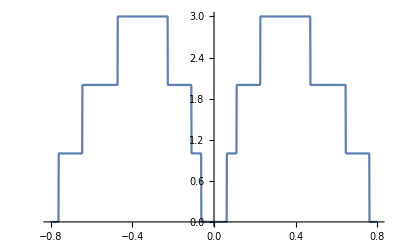

```mathematica
ListPlot[pris,Joined->True]
```

```mathematica
Tally[{imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp}]
```

{{imp,90},{imp5,1},{imp7,1},{imp4,1},{imp10,1},{imp3,1},{imp11,1},{imp2,1},{imp8,1},{imp9,1},{imp6,1}}

```mathematica
ca2[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{gg=g[ω,δ,t,ϵ,m],Tin=T1[t,m],T=ρ[t,m],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp2=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]];
imp3=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]];
imp4=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]];
imp5=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]];
imp6=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]];
imp7=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]];
imp8=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]];
imp9=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ9,μ9}}->ω+ⅈ*δ-ϵ1]];
imp10=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ10,μ10}}->ω+ⅈ*δ-ϵ1]];
imp11=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ11,μ11}}->ω+ⅈ*δ-ϵ1]];
imp12=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ12,μ12}}->ω+ⅈ*δ-ϵ1]];
imp13=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ13,μ13}}->ω+ⅈ*δ-ϵ1]];
imp=Inverse[β[ω,δ,t,ϵ,m]];
tra:=Module[{},lista={RandomSample[{imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp}]};
b=Module[{},
sl1= Module[{J=SR[ω,δ,t,0,m]},Do[J=Inverse[IdentityMatrix[2m]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[2m]-sl1.T.SR[ω,δ,t,0,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,0,m].T.sl1.T].SR[ω,δ,t,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,0,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,δ,t,ϵ,m],tr[ω,δ,t,ϵ,m],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b];tra]
```

```mathematica
Table[{ω,Mean[Table[ca2[ω,0.0001,0.267,0,0.42,7],1000]]},{ω,Range[-0.8,0.8,0.01]}]
```

{{-0.8,1.48304×10^-6},{-0.79,2.64387×10^-6},{-0.78,5.99439×10^-6},{-0.77,0.0000248827},{-0.76,0.391477},{-0.75,0.39175},{-0.74,0.440432},{-0.73,0.480009},{-0.72,0.536313},{-0.71,0.595366},{-0.7,0.618357},{-0.69,0.654684},{-0.68,0.681883},{-0.67,0.711539},{-0.66,0.751207},{-0.65,0.783382},{-0.64,0.773655},{-0.63,0.796513},{-0.62,0.849982},{-0.61,0.916531},{-0.6,0.956196},{-0.59,1.01411},{-0.58,1.06253},{-0.57,1.08943},{-0.56,1.1453},{-0.55,1.16382},{-0.54,1.22153},{-0.53,1.24726},{-0.52,1.28827},{-0.51,1.32369},{-0.5,1.37573},{-0.49,1.4383},{-0.48,1.52289},{-0.47,1.17933},{-0.46,0.899041},{-0.45,1.01229},{-0.44,1.06224},{-0.43,1.13211},{-0.42,1.16324},{-0.41,1.20766},{-0.4,1.24234},{-0.39,1.27428},{-0.38,1.29562},{-0.37,1.35285},{-0.36,1.36649},{-0.35,1.37644},{-0.34,1.40755},{-0.33,1.43409},{-0.32,1.44353},{-0.31,1.47209},{-0.3,1.49552},{-0.29,1.48862},{-0.28,1.53555},{-0.27,1.47059},{-0.26,1.39626},{-0.25,1.06148},{-0.24,0.626985},{-0.23,1.09593},{-0.22,0.541928},{-0.21,0.420797},{-0.2,0.370247},{-0.19,0.366967},{-0.18,0.384483},{-0.17,0.424477},{-0.16,0.467103},{-0.15,0.468929},{-0.14,0.487651},{-0.13,0.524711},{-0.12,0.694925},{-0.11,0.646385},{-0.1,0.368767},{-0.09,0.292536},{-0.08,0.301909},{-0.07,0.281254},{-0.06,0.000356383},{-0.05,0.0000214781},{-0.04,9.05418×10^-6},{-0.03,5.7416×10^-6},{-0.02,4.47534×10^-6},{-0.01,3.88509×10^-6},{0.,3.90195×10^-6},{0.01,3.89962×10^-6},{0.02,4.45002×10^-6},{0.03,5.752×10^-6},{0.04,8.74634×10^-6},{0.05,0.0000207766},{0.06,0.000320802},{0.07,0.396205},{0.08,0.496068},{0.09,0.554689},{0.1,0.612032},{0.11,0.531546},{0.12,0.649372},{0.13,0.692498},{0.14,0.780547},{0.15,0.887379},{0.16,0.99556},{0.17,1.0642},{0.18,1.11086},{0.19,1.17922},{0.2,1.23098},{0.21,1.30881},{0.22,1.37675},{0.23,0.918897},{0.24,1.01375},{0.25,1.20039},{0.26,1.39162},{0.27,1.48786},{0.28,1.46023},{0.29,1.24811},{0.3,0.886767},{0.31,0.619117},{0.32,0.544231},{0.33,0.531794},{0.34,0.570368},{0.35,0.630827},{0.36,0.666115},{0.37,0.716309},{0.38,0.755593},{0.39,0.762696},{0.4,0.794011},{0.41,0.787363},{0.42,0.783119},{0.43,0.742683},{0.44,0.718319},{0.45,0.692744},{0.46,0.696238},{0.47,1.03795},{0.48,0.542509},{0.49,0.502267},{0.5,0.458219},{0.51,0.390061},{0.52,0.366223},{0.53,0.367745},{0.54,0.363372},{0.55,0.392226},{0.56,0.402147},{0.57,0.428015},{0.58,0.440103},{0.59,0.444597},{0.6,0.454371},{0.61,0.45636},{0.62,0.441707},{0.63,0.461531},{0.64,0.510267},{0.65,0.330133},{0.66,0.176801},{0.67,0.183789},{0.68,0.156649},{0.69,0.141588},{0.7,0.134023},{0.71,0.145507},{0.72,0.151264},{0.73,0.158523},{0.74,0.174141},{0.75,0.188356},{0.76,0.302609},{0.77,0.000024523},{0.78,5.92695×10^-6},{0.79,2.63418×10^-6},{0.8,1.4563×10^-6}}

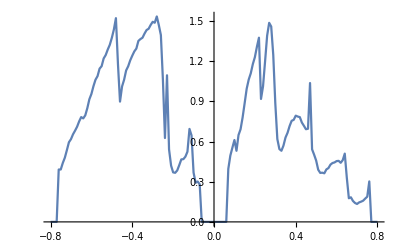

```mathematica
ListPlot[%20,Joined->True]
```

```mathematica
Export["10impdft.dat",%20]
```

10impdft.dat

```mathematica
Import["10impdft.dat"][[13;;102]]
```

{{-0.68,0.681883},{-0.67,0.711539},{-0.66,0.751207},{-0.65,0.783382},{-0.64,0.773655},{-0.63,0.796513},{-0.62,0.849982},{-0.61,0.916531},{-0.6,0.956196},{-0.59,1.01411},{-0.58,1.06253},{-0.57,1.08943},{-0.56,1.1453},{-0.55,1.16382},{-0.54,1.22153},{-0.53,1.24726},{-0.52,1.28827},{-0.51,1.32369},{-0.5,1.37573},{-0.49,1.4383},{-0.48,1.52289},{-0.47,1.17933},{-0.46,0.899041},{-0.45,1.01229},{-0.44,1.06224},{-0.43,1.13211},{-0.42,1.16324},{-0.41,1.20766},{-0.4,1.24234},{-0.39,1.27428},{-0.38,1.29562},{-0.37,1.35285},{-0.36,1.36649},{-0.35,1.37644},{-0.34,1.40755},{-0.33,1.43409},{-0.32,1.44353},{-0.31,1.47209},{-0.3,1.49552},{-0.29,1.48862},{-0.28,1.53555},{-0.27,1.47059},{-0.26,1.39626},{-0.25,1.06148},{-0.24,0.626985},{-0.23,1.09593},{-0.22,0.541928},{-0.21,0.420797},{-0.2,0.370247},{-0.19,0.366967},{-0.18,0.384483},{-0.17,0.424477},{-0.16,0.467103},{-0.15,0.468929},{-0.14,0.487651},{-0.13,0.524711},{-0.12,0.694925},{-0.11,0.646385},{-0.1,0.368767},{-0.09,0.292536},{-0.08,0.301909},{-0.07,0.281254},{-0.06,0.000356383},{-0.05,0.0000214781},{-0.04,9.05418×10^-6},{-0.03,5.7416×10^-6},{-0.02,4.47534×10^-6},{-0.01,3.88509×10^-6},{0.,3.90195×10^-6},{0.01,3.89962×10^-6},{0.02,4.45002×10^-6},{0.03,5.752×10^-6},{0.04,8.74634×10^-6},{0.05,0.0000207766},{0.06,0.000320802},{0.07,0.396205},{0.08,0.496068},{0.09,0.554689},{0.1,0.612032},{0.11,0.531546},{0.12,0.649372},{0.13,0.692498},{0.14,0.780547},{0.15,0.887379},{0.16,0.99556},{0.17,1.0642},{0.18,1.11086},{0.19,1.17922},{0.2,1.23098},{0.21,1.30881}}

```mathematica
Table[{x,Interpolation[Import["10impdft.dat"][[13;;102]]][x]},{x,Range[-0.68,0.2,0.89/445]}]
```

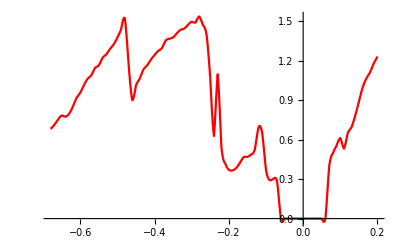

```mathematica
ListPlot[%25,Joined->True,PlotStyle->Red]
```

```mathematica
ca1imp[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{gg=g[ω,δ,t,ϵ,m],Tin=T1[t,m],T=ρ[t,m],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp2=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]];
imp3=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ2,μ2}}->ω+ⅈ*δ-ϵ]];
imp4=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ3,μ3}}->ω+ⅈ*δ-ϵ]];
imp5=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ4,μ4}}->ω+ⅈ*δ-ϵ]];
imp6=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ6,μ6}}->ω+ⅈ*δ-ϵ]];
imp7=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ7,μ7}}->ω+ⅈ*δ-ϵ]];
imp8=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ8,μ8}}->ω+ⅈ*δ-ϵ]];
imp9=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ9,μ9}}->ω+ⅈ*δ-ϵ]];
imp10=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ10,μ10}}->ω+ⅈ*δ-ϵ]];
imp11=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ11,μ11}}->ω+ⅈ*δ-ϵ]];
imp12=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ12,μ12}}->ω+ⅈ*δ-ϵ]];
imp13=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ13,μ13}}->ω+ⅈ*δ-ϵ]];
imp=Inverse[β[ω,δ,t,ϵ,m]];
tra:=Module[{},lista={RandomSample[{imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp}]};
b=Module[{},
sl1= Module[{J=SR[ω,δ,t,0,m]},Do[J=Inverse[IdentityMatrix[2m]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[2m]-sl1.T.SR[ω,δ,t,0,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,0,m].T.sl1.T].SR[ω,δ,t,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,0,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,δ,t,ϵ,m],tr[ω,δ,t,ϵ,m],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b];tra]
```

```mathematica
Table[{ω,Mean[Table[ca1imp[ω,0.0001,0.267,0,0.42,7],1000]]},{ω,Range[-0.68,0.2,0.01]}]
```

{{-0.68,0.953976},{-0.67,0.959133},{-0.66,0.967292},{-0.65,0.976266},{-0.64,1.65963},{-0.63,1.69359},{-0.62,1.7427},{-0.61,1.77198},{-0.6,1.80015},{-0.59,1.81754},{-0.58,1.82708},{-0.57,1.84786},{-0.56,1.8564},{-0.55,1.86612},{-0.54,1.87755},{-0.53,1.88327},{-0.52,1.88976},{-0.51,1.89957},{-0.5,1.91341},{-0.49,1.92829},{-0.48,1.94272},{-0.47,2.45828},{-0.46,2.4314},{-0.45,2.50671},{-0.44,2.54265},{-0.43,2.58726},{-0.42,2.60869},{-0.41,2.6195},{-0.4,2.63412},{-0.39,2.65577},{-0.38,2.67005},{-0.37,2.68303},{-0.36,2.69282},{-0.35,2.70029},{-0.34,2.72347},{-0.33,2.71904},{-0.32,2.73061},{-0.31,2.74109},{-0.3,2.75209},{-0.29,2.75749},{-0.28,2.77191},{-0.27,2.76594},{-0.26,2.72566},{-0.25,2.64322},{-0.24,2.32878},{-0.23,1.79694},{-0.22,1.41825},{-0.21,1.41781},{-0.2,1.33566},{-0.19,1.34941},{-0.18,1.45464},{-0.17,1.52141},{-0.16,1.55609},{-0.15,1.56995},{-0.14,1.56339},{-0.13,1.51289},{-0.12,1.36968},{-0.11,0.845653},{-0.1,0.691339},{-0.09,0.781561},{-0.08,0.790047},{-0.07,0.738823},{-0.06,0.000373981},{-0.05,0.00002227},{-0.04,9.31076×10^-6},{-0.03,5.94157×10^-6},{-0.02,4.63532×10^-6},{-0.01,4.07808×10^-6},{0.,3.92767×10^-6},{0.01,4.06848×10^-6},{0.02,4.63271×10^-6},{0.03,5.95644×10^-6},{0.04,9.28371×10^-6},{0.05,0.0000221515},{0.06,0.000372263},{0.07,0.859962},{0.08,0.908581},{0.09,0.926539},{0.1,0.937511},{0.11,0.923962},{0.12,1.61399},{0.13,1.73602},{0.14,1.77753},{0.15,1.80671},{0.16,1.83244},{0.17,1.84424},{0.18,1.86252},{0.19,1.87016},{0.2,1.88828}}

```mathematica
Export["1impdft.dat",%30]
```

1impdft.dat

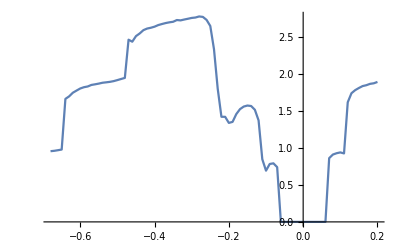

```mathematica
ListPlot[%30,Joined->True]
```

```mathematica
7*16
```

112